```mathematica
(*  AQC // Matthew Berntson //  4/12/16 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
sz={{1,0},{0,-1}};
sx={{0,1},{1,0}};
ID=IdentityMatrix[2];
```

### Example for the Facility Location problem, using an Ising Hamiltonian derived from a binary programming formulation. For the Ising Hamiltonian, the spin couplings: J_{ij} = 2*A*Sum_{j=1}^m S_ji S_jl for i!=j, and J_{ii} = A*Sum_{j=1}^m S_ji^2 for i==j . The magnetic field parameters: h_{i} = B*c_i + 2*A*Sum_{j=1}^m b_j S_ji.

```mathematica
(* The data for the matrices of cost (c), coupling (S), and constraint (b) are as follows *)
```

```mathematica
(* Number of binary variables *)
```

```mathematica
Num=5;
```

```mathematica
(* Number of constraints *)
```

```mathematica
m=1;
```

```mathematica
(* constants A and B are dictated by Num, s.t. A/B~>N *)
```

```mathematica
A=Num;
B=1;
```

```mathematica
(* c is the cost vector (want to maximize so use +1) *)
```

```mathematica
c = 1*{9,5,6,4,0};
```

```mathematica
(* S is the matrix of constraints (lhs) for the system of eqns *)
```

```mathematica
S ={{6,3,5,2,-1}};
```

```mathematica
(* b is the array of constraints (rhs) *)
```

```mathematica
b ={10};
```

```mathematica
(* Now calculate coupling and field parameters *)
```

```mathematica
(* Field Parameters *)
```

```mathematica
h={0,0,0,0,0};
```

```mathematica
For[i=1,i<Num+1,i++,h[[i]]=B*c[[i]]+2*A*Sum[b[[j]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[h]
```

(609
305
506
204
-100)

```mathematica
(* Coupling Terms *)
```

```mathematica
J={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
```

```mathematica
(* Calculate all elements using the i≠l formula *)
```

```mathematica
For[l=1,l<Num+1,l++,For[i=l,i<Num+1,i++,J[[l]][[i]]=2*A*Sum[S[[j]][[i]]*S[[j]][[l]],{j,m}]]]
```

```mathematica
MatrixForm[J]
```

(360 | 180 | 300 | 120 | -60
0 | 90 | 150 | 60 | -30
0 | 0 | 250 | 100 | -50
0 | 0 | 0 | 40 | -20
0 | 0 | 0 | 0 | 10)

```mathematica
(* Replace diagonal elements with i==j formula *)
```

```mathematica
For[i=1,i<Num+1,i++,J[[i]][[i]]=A*Sum[S[[j]][[i]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[J]
```

(180 | 180 | 300 | 120 | -60
0 | 45 | 150 | 60 | -30
0 | 0 | 125 | 100 | -50
0 | 0 | 0 | 20 | -20
0 | 0 | 0 | 0 | 5)

```mathematica
(* Hard code the spins *)
```

```mathematica
(* Note that the spins for the diagonal coupling terms are z_{i}^2 *)
```

```mathematica
x1=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
x2=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
x3=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];
```

```mathematica
x4=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];
```

```mathematica
x5=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];
```

```mathematica
z12=KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z13=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z14=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z15=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];
```

```mathematica
z23=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z24=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z25=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,ID]]]];
```

```mathematica
z35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,sz]]]];
```

```mathematica
(* Add field terms to problem hamiltonian *)
```

```mathematica
hp=-1*(h[[1]]x1+h[[2]]x2+h[[3]]x3+h[[4]]x4+h[[5]]x5);
```

```mathematica
(* Add coupling terms to problem hamiltonian *)
```

```mathematica
ID32=IdentityMatrix[32];
```

```mathematica
hp+=-1*(J[[1]][[1]]ID32+J[[1]][[2]] z12+J[[1]][[3]] z13+J[[1]][[4]] z14+J[[1]][[5]]z15+J[[2]][[2]]ID32+J[[2]][[3]]z23+J[[2]][[4]]z24+J[[2]][[5]]z25+J[[3]][[3]]ID32+J[[3]][[4]]z34+J[[3]][[5]]z35+J[[4]][[4]]ID32+J[[4]][[5]]z45+J[[5]][[5]]ID32);
```

```mathematica
MatrixForm[hp]
```

(-1125 | 100 | -204 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
100 | -1445 | 0 | -204 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-204 | 0 | -605 | 100 | 0 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -204 | 100 | -845 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-506 | 0 | 0 | 0 | -125 | 100 | -204 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -506 | 0 | 0 | 100 | -245 | 0 | -204 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -506 | 0 | -204 | 0 | -5 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -506 | 0 | -204 | 100 | -45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -405 | 100 | -204 | 0 | -506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | -605 | 0 | -204 | 0 | -506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | -204 | 0 | -125 | 100 | 0 | 0 | -506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | -204 | 100 | -245 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | -5 | 100 | -204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | 0 | 100 | -5 | 0 | -204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | -204 | 0 | -125 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | -204 | 100 | -45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609
-609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -45 | 100 | -204 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | -125 | 0 | -204 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -204 | 0 | -5 | 100 | 0 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -204 | 100 | -5 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | -245 | 100 | -204 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -506 | 0 | 0 | 100 | -125 | 0 | -204 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -506 | 0 | -204 | 0 | -605 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -506 | 0 | -204 | 100 | -405 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -45 | 100 | -204 | 0 | -506 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | -5 | 0 | -204 | 0 | -506 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | -204 | 0 | -245 | 100 | 0 | 0 | -506 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | 0 | 0 | -204 | 100 | -125 | 0 | 0 | 0 | -506
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | 0 | 0 | -845 | 100 | -204 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | 0 | 100 | -605 | 0 | -204
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | -204 | 0 | -1445 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -305 | 0 | 0 | 0 | -506 | 0 | -204 | 100 | -1125)

```mathematica
x12=KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x13=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x14=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];;
```

```mathematica
x15=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];;
```

```mathematica
x23=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];
```

```mathematica
x24=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];
```

```mathematica
x25=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];
```

```mathematica
x34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,ID]]]];
```

```mathematica
x35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,sx]]]];
```

```mathematica
x45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,sx]]]];
```

```mathematica
(* Scaling by X100 in order to see gap *)
```

```mathematica
hinit=-1*100*(x12+x13+x14+x15+x23+x24+x25+x34+x35+x45) ;(* placeholder initial Hamiltonian, something simpler would be more practical *)
```

```mathematica
MatrixForm[hinit]
```

(0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0
0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0
-100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0
0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0
-100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0
-100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0
0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100
0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0
-100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0
-100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0
0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100
-100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0
0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100
0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100
0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0
0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0
-100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0
-100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0
0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100
-100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0
0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100
0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100
0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0
-100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0
0 | -100 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100
0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100
0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0
0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100
0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0
0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0 | -100 | -100 | 0 | 0 | -100 | 0 | -100 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | 0 | 0 | -100 | 0 | -100 | -100 | 0 | 0 | -100 | -100 | 0 | -100 | 0 | 0 | 0)

```mathematica
Eigenvalues[hinit]
```

{-1000,-1000,-200,-200,-200,-200,-200,-200,-200,-200,-200,-200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200}

```mathematica
htot[s_]:=s hp+(1-s) hinit
```

```mathematica
MatrixForm[htot[s]]
```

(-1125 s | 100 s | -204 s | -100 (1-s) | -506 s | -100 (1-s) | -100 (1-s) | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | 0
100 s | -1445 s | -100 (1-s) | -204 s | -100 (1-s) | -506 s | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0
-204 s | -100 (1-s) | -605 s | 100 s | -100 (1-s) | 0 | -506 s | -100 (1-s) | -100 (1-s) | 0 | -305 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0
-100 (1-s) | -204 s | 100 s | -845 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0
-506 s | -100 (1-s) | -100 (1-s) | 0 | -125 s | 100 s | -204 s | -100 (1-s) | -100 (1-s) | 0 | 0 | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0
-100 (1-s) | -506 s | 0 | -100 (1-s) | 100 s | -245 s | -100 (1-s) | -204 s | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -305 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0
-100 (1-s) | 0 | -506 s | -100 (1-s) | -204 s | -100 (1-s) | -5 s | 100 s | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -305 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0
0 | -100 (1-s) | -100 (1-s) | -506 s | -100 (1-s) | -204 s | 100 s | -45 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s)
-305 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -405 s | 100 s | -204 s | -100 (1-s) | -506 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0
-100 (1-s) | -305 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 100 s | -605 s | -100 (1-s) | -204 s | -100 (1-s) | -506 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0
-100 (1-s) | 0 | -305 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -204 s | -100 (1-s) | -125 s | 100 s | -100 (1-s) | 0 | -506 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0
0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | 0 | 0 | -100 (1-s) | -100 (1-s) | -204 s | 100 s | -245 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | -100 (1-s)
-100 (1-s) | 0 | 0 | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -506 s | -100 (1-s) | -100 (1-s) | 0 | -5 s | 100 s | -204 s | -100 (1-s) | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0
0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -305 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | 0 | -100 (1-s) | 100 s | -5 s | -100 (1-s) | -204 s | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s)
0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -506 s | -100 (1-s) | -204 s | -100 (1-s) | -125 s | 100 s | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s)
0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | -100 (1-s) | -204 s | 100 s | -45 s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -609 s
-609 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -45 s | 100 s | -204 s | -100 (1-s) | -506 s | -100 (1-s) | -100 (1-s) | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0
-100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | 100 s | -125 s | -100 (1-s) | -204 s | -100 (1-s) | -506 s | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0
-100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -204 s | -100 (1-s) | -5 s | 100 s | -100 (1-s) | 0 | -506 s | -100 (1-s) | -100 (1-s) | 0 | -305 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0
0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | -100 (1-s) | -204 s | 100 s | -5 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | 0 | 0 | -100 (1-s)
-100 (1-s) | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -506 s | -100 (1-s) | -100 (1-s) | 0 | -245 s | 100 s | -204 s | -100 (1-s) | -100 (1-s) | 0 | 0 | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0
0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -506 s | 0 | -100 (1-s) | 100 s | -125 s | -100 (1-s) | -204 s | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -305 s | 0 | -100 (1-s)
0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -506 s | -100 (1-s) | -204 s | -100 (1-s) | -605 s | 100 s | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -305 s | -100 (1-s)
0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -506 s | -100 (1-s) | -204 s | 100 s | -405 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -305 s
-100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -45 s | 100 s | -204 s | -100 (1-s) | -506 s | -100 (1-s) | -100 (1-s) | 0
0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -305 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 100 s | -5 s | -100 (1-s) | -204 s | -100 (1-s) | -506 s | 0 | -100 (1-s)
0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -305 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -204 s | -100 (1-s) | -245 s | 100 s | -100 (1-s) | 0 | -506 s | -100 (1-s)
0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | 0 | 0 | -100 (1-s) | -100 (1-s) | -204 s | 100 s | -125 s | 0 | -100 (1-s) | -100 (1-s) | -506 s
0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -609 s | -100 (1-s) | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -506 s | -100 (1-s) | -100 (1-s) | 0 | -845 s | 100 s | -204 s | -100 (1-s)
0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -609 s | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | 0 | -100 (1-s) | -305 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | 0 | -100 (1-s) | 100 s | -605 s | -100 (1-s) | -204 s
0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -609 s | -100 (1-s) | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | 0 | -305 s | -100 (1-s) | -100 (1-s) | 0 | -506 s | -100 (1-s) | -204 s | -100 (1-s) | -1445 s | 100 s
0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 (1-s) | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -609 s | 0 | 0 | 0 | -100 (1-s) | 0 | -100 (1-s) | -100 (1-s) | -305 s | 0 | -100 (1-s) | -100 (1-s) | -506 s | -100 (1-s) | -204 s | 100 s | -1125 s)

```mathematica
(* Sort the eigensystem *)
```

```mathematica
evals[s_]=Eigenvalues[htot[s]]
```

```mathematica
SortEigensystem[eigsys_]:=Transpose@SortBy[Transpose[eigsys],First]
```

```mathematica
eigsys=Table[SortEigensystem[Eigensystem[htot[s]]//N],{s,0,1,.01}];
```

```mathematica
(* Propagator, initial is the initial ground state *)
```

```mathematica
T=100;
expectation=Table[0,{i,1,T}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-993.75,-987.528,-981.37,-975.2,-969.053,-962.907,-956.926,-950.939,-944.969,-939.187,-933.336,-927.625,-921.863,-916.107,-910.707,-905.096,-899.656,-895.052,-890.156,-888.496,-895.379,-905.875,-915.81,-928.841,-941.682,-954.902,-968.266,-981.616,-994.686,-1008.14,-1021.41,-1035.26,-1049.16,-1063.19,-1077.12,-1091.18,-1105.47,-1119.74,-1133.94,-1148.31,-1162.63,-1177.26,-1191.6,-1206.15,-1220.44,-1235.04,-1249.38,-1264.2,-1278.72,-1293.59,-1308.29,-1323.06,-1337.5,-1352.18,-1366.9,-1381.48,-1396.06,-1410.77,-1425.59,-1440.45,-1455.11,-1470.,-1484.84,-1499.8,-1514.47,-1529.85,-1544.89,-1559.79,-1574.67,-1589.62,-1604.66,-1619.87,-1635.04,-1650.29,-1665.4,-1680.63,-1696.1,-1711.56,-1726.78,-1742.35,-1758.06,-1773.36,-1789.,-1804.63,-1820.32,-1836.07,-1851.96,-1868.17,-1884.17,-1900.11,-1916.07,-1932.33,-1948.56,-1965.16,-1981.64,-1997.96,-2014.49,-2031.32,-2048.55,0}

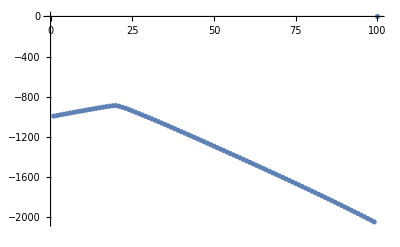

(-0.0911311+0.0991271 ⅈ
0.0451869-0.290563 ⅈ
-0.173959-0.0493858 ⅈ
0.0682115-0.241364 ⅈ
-0.0500804+0.0437438 ⅈ
0.0474402-0.149002 ⅈ
-0.115129-0.0694204 ⅈ
0.060946-0.155799 ⅈ
-0.138636+0.0624232 ⅈ
0.0396003-0.109602 ⅈ
-0.13816-0.0558972 ⅈ
0.00314403-0.127488 ⅈ
-0.11938+0.0283086 ⅈ
0.0632948-0.0794356 ⅈ
-0.154058-0.126063 ⅈ
0.0115353-0.115039 ⅈ
-0.062151+0.0418753 ⅈ
0.0405971-0.152173 ⅈ
-0.123614-0.0681554 ⅈ
0.0535982-0.163446 ⅈ
-0.0582012+0.0241197 ⅈ
0.0613147-0.124669 ⅈ
-0.157496-0.132044 ⅈ
0.0732709-0.178561 ⅈ
-0.12042+0.0318759 ⅈ
0.0523939-0.0820036 ⅈ
-0.156461-0.118522 ⅈ
0.00953236-0.119592 ⅈ
-0.195858+0.00680131 ⅈ
0.103136-0.103347 ⅈ
-0.315526-0.333089 ⅈ
0.0332418-0.198445 ⅈ)

```mathematica
initial=eigsys[[1]][[2]][[1]];
MatrixForm[initial];
For[i=0,i<T,i++,
nv=MatrixExp[-I*htot[i/T],initial]//N;
expectation[[i]]=Re[Conjugate[nv].htot[i/T].nv];
initial = nv;
];
expectation=Table[expectation[[i]],{i,1,Length[expectation]}]
ListPlot[expectation]
MatrixForm[initial]
```

```mathematica
(* ListPlot the eigensystem
```

```mathematica
eigsys[[All,1,1]];
```

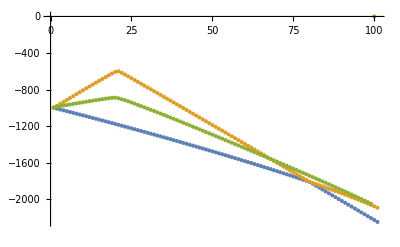

```mathematica
ListPlot[{eigsys[[All,1,1]],eigsys[[All,1,2]],expectation}]
```

```mathematica
(* Ground state of the final hamiltonian (s=1) *)
```

```mathematica
eigsys[[-1,2,1]]
```

{-0.223898,0.392042,-0.147116,0.190554,-0.126623,0.176685,-0.123232,0.120462,-0.134614,0.179489,-0.133421,0.124432,-0.121072,0.121373,-0.179568,0.126549,-0.126549,0.179568,-0.121373,0.121072,-0.124432,0.133421,-0.179489,0.134614,-0.120462,0.123232,-0.176685,0.126623,-0.190554,0.147116,-0.392042,0.223898}

```mathematica
up={{1},{0}};
down={{0},{1}};
MatrixForm[up]
MatrixForm[down]
```

(1
0)

(0
1)

```mathematica
MatrixForm[KroneckerProduct[up,KroneckerProduct[up,KroneckerProduct[up,KroneckerProduct[up,down]]]]]
```

(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
(* This is the same state as the ground state of the final hamiltonian *)
```

```mathematica
(* Therefore the solution using this method is x1=x2=x3=x4=1, x5=0.  This is unfortunate, as these values clearly do not meet the equality constraint.  Perhaps there is an error in building the problem Hamiltonian *)
```